```mathematica
Quiet[Remove["Global`*"],{Remove::rmnsm}];Print["Mathematica $Version = “",$Version,"”"];Print["Execution time = ",DateString[DateList[],{"Hour",":","Minute"," on ","DayNameShort"," ","Day"," ","MonthNameShort"," ","Year"}]];
```

Mathematica $Version = “9.0 for Mac OS X x86 (64-bit) (January 24, 2013)”

Execution time = 16:28 on Sun 06 Nov 2022

```mathematica
Preliminaries
```

```mathematica
simplifyExtra:=Simplify[PowerExpand[Simplify[#]]]&;
```

```mathematica
KnotsFromCoeffs[{c0_:0,c1_:0,c2_:0,c3_:0}]={c0,c0+c1/3,c0+(2c1+c2)/3,c0+c1+c2+c3};
CoeffsFromKnots[{z0_,z1_,z2_,z3_}]=PadRight[{z0,-3 z0+3 z1,3 z0-6 z1+3 z2,-z0+3 z1-3 z2+z3},4];
CoeffsBezierSplit[coeffs_List,t0_,t1_]:=Module[{t},(PadRight[CoefficientList[Table[(t0*(1-t)+t1*t)^i,{i,0,3}].PadRight[coeffs,4,0],t],4,0])//simplifyExtra];
KnotsBezierSplit[{z0_,z1_,z2_,z3_},t0_,t1_]:=KnotsFromCoeffs[CoeffsBezierSplit[CoeffsFromKnots[{z0,z1,z2,z3}],t0,t1]]//simplifyExtra;
```

```mathematica
pathAdjacent[({{x0_, x1_, x2_, x3_}, {y0_, y1_, y2_, y3_}}),dist_]:=Module[{t,x,y,dx,dy},
	x=CoeffsFromKnots[{x0,x1,x2,x3}].{1,t,t^2,t^3};
	y=CoeffsFromKnots[{y0,y1,y2,y3}].{1,t,t^2,t^3};
	dx=D[x,t];
	dy=D[y,t];
	Return[{
		x+dist dy/Sqrt[dx^2+dy^2],
		y-dist dx/Sqrt[dx^2+dy^2]
	}/.{t->#}&];
];
```

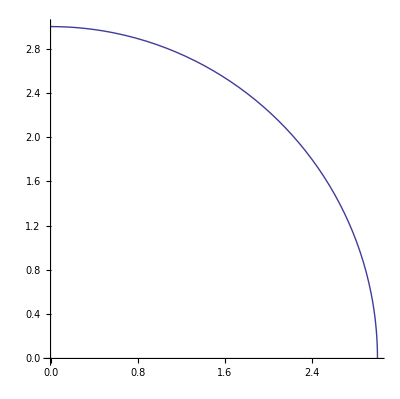

```mathematica
pathAdjacent[({{1, 1, 11/20, 0}, {0, 11/20, 1, 1}}),2]//simplifyExtra;
ParametricPlot[%[z],{z,0,1}]
```

```mathematica
pathOffsetIntersect[knots1_List,knots2_List,dist_,tGuess1_:1/2, tGuess2_:1/2]:=Module[{p1,p2,t1,t2,slv},
	p1[t1_]=pathAdjacent[knots1,dist][t1]//simplifyExtra;
	p2[t2_]=pathAdjacent[knots2,dist][t2]//simplifyExtra;
	slv=FindRoot[(p1[t1]==p2[t2]),{{t1,tGuess1},{t2,tGuess2}},WorkingPrecision->48];
	If[ Length[slv]==0 ,Return["pathOffsetIntersect: no intersection."]];
	{t1,t2}=({t1,t2}/.slv)//simplifyExtra;
	If[And[LeafCount[t1]>64,NumericQ[t1],Head[t1]=!=Real],t1=N[t1,64]];
	If[And[LeafCount[t2]>64,NumericQ[t2],Head[t2]=!=Real],t2=N[t2,64]];
	Return[{t1,t2}];
];
```

```mathematica
pathOffsetIntersect[({{3, 3, 3, 3}, {0, 1, 2, 3}}),({{3, 0, 0, 2}, {2, 0, 0, 3}}),-2/10]
```

{0.542124398165218633771648080434171929572523429286,0.035816803795296131889055438557931688646432566831}

```mathematica
approximationKnots[xy_,tStart_:0,tEnd_:1,speedGuess1_:0.33333,speedGuess2_:0.33333]:=Module[{x0,y0,x1,y1,x2,y2,x3,y3,t,dxy,d0x,d0y,d1x,d1y,dd0x,dd0y,dd1x,dd1y,s1,s2,curvature0Function,curvature1Function,curvature0Bezier,curvature1Bezier,slv},
	Assuming[{x0∈Reals,y0∈Reals,x1∈Reals,y1∈Reals,x2∈Reals,y2∈Reals,x3∈Reals,y3∈Reals,t∈Reals,dxy∈Reals,d0x∈Reals,d0y∈Reals,d1x∈Reals,d1y∈Reals,dd0x∈Reals,dd0y∈Reals,dd1x∈Reals,dd1y∈Reals,s1∈Reals,s2∈Reals,curvature0Function∈Reals,curvature1Function∈Reals,curvature0Bezier∈Reals,curvature1Bezier∈Reals,ForAll[t,xy[t]⟦1⟧∈Reals&&xy[t]⟦2⟧∈Reals],(t-tStart)(t-tEnd)≤0},
		{x0,y0}=xy[tStart];
		{x3,y3}=xy[tEnd];
		dxy=D[xy[t],t]//Simplify;
		{{d0x,d0y},{d1x,d1y}}=FullSimplify[dxy/.{{t->tStart},{t->tEnd}}];
		{{dd0x,dd0y},{dd1x,dd1y}}=FullSimplify[D[dxy,t]/.{{t->tStart},{t->tEnd}}];
		Remove[dxy];
		x1=(x0+d0x s1)//FullSimplify;
		y1=(y0+d0y s1)//FullSimplify;
		x2=(x3-d1x s2)//FullSimplify;
		y2=(y3-d1y s2)//FullSimplify;
		curvature0Function=((d0x^2+d0y^2)^(3/2))/(d0x dd0y-d0y dd0x)//FullSimplify;
		curvature1Function=((d1x^2+d1y^2)^(3/2))/(d1x dd1y-d1y dd1x)//FullSimplify;
		Remove[dd0x,dd0y,dd1x,dd1y];
		If[And[LeafCount[curvature0Function]>64,NumericQ[curvature0Function],Head[curvature0Function]=!=Real],curvature0Function=Chop[N[curvature0Function,64],10^-32]];
		If[And[LeafCount[curvature1Function]>64,NumericQ[curvature1Function],Head[curvature1Function]=!=Real],curvature1Function=Chop[N[curvature1Function,64],10^-32]];
		curvature0Bezier=Chop[(-3 ((x0-x1)^2+(y0-y1)^2)^(3/2))/(2 (x0 (y2-y1)+x1 (y0-y2)+x2 (y1-y0)))//Simplify,10^-32]//FullSimplify;
		curvature1Bezier=Chop[(-3 ((x2-x3)^2+(y2-y3)^2)^(3/2))/(2 (x3 (y2-y1)+x2 (y1-y3)+x1 (y3-y2)))//Simplify,10^-32]//FullSimplify;
		Print["curvature0Function = ",curvature0Function," ≈ ",curvature0Function//N];
		Print["curvature1Function = ",curvature1Function," ≈ ",curvature1Function//N];
		Print["curvature0Bezier = ",curvature0Bezier," ≈ ",curvature0Bezier//N];
		Print["curvature1Bezier = ",curvature1Bezier," ≈ ",curvature1Bezier//N];
		(* slv=Apply[
			If[Head[curvature0Function]===Real || Head[curvature1Function]===Real,NSolve,Solve],
			{
				{
					curvature0Function==curvature0Bezier,
					curvature1Function==curvature1Bezier,
					If[tEnd≥tStart,(s1≥0)&&(s2≥0),(s1≤0)&&(s2≤0)]
				},
				{s1,s2},Reals
			}
		]; *)
		slv=FindRoot[
			{
				curvature0Function-curvature0Bezier,
				curvature1Function-curvature1Bezier (*,
				If[tEnd≥tStart,(s1≥0)&&(s2≥0),(s1≤0)&&(s2≤0)]  *)
			},{
				{s1,speedGuess1*Sqrt[((x0-x3)^2+(y0-y3)^2)/(d0x^2+d0y^2)]},
				{s2,speedGuess2*Sqrt[((x0-x3)^2+(y0-y3)^2)/(d1x^2+d1y^2)]}
			},WorkingPrecision->18
		];
		Remove[d0x,d0y,d1x,d1y];
		Print["slv = ",slv," ≈ ",slv//N];
		If[ Length[slv]==0 ,Return["approximationKnots: no solution for speeds."]];
		(* {s1,s2}=Simplify[({s1,s2}/.Sort[slv,((s1^2+s2^2)/.#1)≤((s1^2+s2^2)/.#2)&]⟦1⟧)]; *)
		{s1,s2}=Simplify[{s1,s2}/.slv];
		(* If[And[LeafCount[s1]>64,NumericQ[s1],Head[s1]=!=Real],s1=N[s1,64]]; *)
		(*If[And[LeafCount[s2]>64,NumericQ[s2],Head[s2]=!=Real],s2=N[s2,64]]; *)
		Return[({{x0, x1, x2, x3}, {y0, y1, y2, y3}})//Simplify];
	]
]
```

```mathematica
approximationKnots[{Cos[#],Sin[#]}&,0,π/2]//MatrixForm
```

curvature0Function = 1 ≈ 1.

curvature1Function = 1 ≈ 1.

curvature0Bezier = (3 s1$319 Abs[s1$319])/(2-2 s2$319) ≈ (3. s1$319 Abs[s1$319])/(2.-2. s2$319)

curvature1Bezier = (3 s2$319 Abs[s2$319])/(2-2 s1$319) ≈ (3. s2$319 Abs[s2$319])/(2.-2. s1$319)

slv = {s1$319→0.548583770354863475,s2$319→0.548583770354863563} ≈ {s1$319→0.548584,s2$319→0.548584}

(1 | 1 | 0.548583770354863563 | 0
0 | 0.548583770354863475 | 1 | 1)

```mathematica
IQD
```

```mathematica
knotsOrig=({{-9*8, 0, 0, 9*8}, {9*8, z, z, 9*8}});
Print["lineWidth = ",lineWidth=9," ≈ ",lineWidth//N];
Print["gapH = ",gapH=(2*9*8-6lineWidth)/5," ≈ ",gapH//N,".\ngapH/lineWidth = ",gapH/lineWidth," ≈ ",(gapH/lineWidth)//N];
```

lineWidth = 9 ≈ 9.

gapH = 18 ≈ 18..
gapH/lineWidth = 2 ≈ 2.

```mathematica
xOrig[t_]=CoeffsFromKnots[knotsOrig⟦1⟧].{1,t,t^2,t^3};
yOrig[t_]=CoeffsFromKnots[knotsOrig⟦2⟧].{1,t,t^2,t^3};
```

```mathematica
z=8;
```

```mathematica
(yOrig[1/2])//FullSimplify
```

24

```mathematica
(yOrig[t]D[xOrig[t],t])//FullSimplify
```

5184 (1+2 (-1+t) t) (3+8 (-1+t) t)

```mathematica
Integrate[%,{t,0,1}]
```

31104/5

```mathematica
tValues=Table[(
	xL=Simplify[-72+(lineWidth+gapH)*i];
	xR=Simplify[xL+gapH+2lineWidth];
	tL=pathOffsetIntersect[({{xL, xL, xL, xL}, {0, 1, 2, 3}}),knotsOrig,lineWidth,1/4,1/4]⟦2⟧//Simplify;
	tR=pathOffsetIntersect[knotsOrig,({{xR, xR, xR, xR}, {3, 2, 1, 0}}),lineWidth,1/4,1/4]⟦1⟧//Simplify;
	Print["i = ",i,"; xL = ",xL//N,"; xR = ",xR//N,"; tL = ",tL,"; tR = ",tR];
	{tL,tR}
),{i,0,4,1}]
```

i = 0; xL = -72.; xR = -36.; tL = 0.0744104423687361467025529812824509686282035883719; tR = 0.179562313466755793928386850611257258490654947126

i = 1; xL = -45.; xR = -9.; tL = 0.239354233234325373249716929795207908934352376576; tR = 0.369499738804175880061999588792253968668779676064

i = 2; xL = -18.; xR = 18.; tL = 0.435392015351355319656277144380970307083472343322; tR = 0.564607984648644680343722855619029692916527656678

i = 3; xL = 9.; xR = 45.; tL = 0.630500261195824119938000411207746031331220323936; tR = 0.760645766765674626750283070204792091065647623424

i = 4; xL = 36.; xR = 72.; tL = 0.820437686533244206071613149388742741509345052874; tR = 0.925589557631263853297447018717549031371796411628

{{0.0744104423687361467025529812824509686282035883719,0.179562313466755793928386850611257258490654947126},{0.239354233234325373249716929795207908934352376576,0.369499738804175880061999588792253968668779676064},{0.435392015351355319656277144380970307083472343322,0.564607984648644680343722855619029692916527656678},{0.630500261195824119938000411207746031331220323936,0.760645766765674626750283070204792091065647623424},{0.820437686533244206071613149388742741509345052874,0.925589557631263853297447018717549031371796411628}}

```mathematica
Prepend[Map[If[NumericQ[#],{#,xOrig[#],yOrig[#]},{"·","·","·"}]&,tValues//Flatten],{"t","xOrig","yOrig"}]//N//MatrixForm
```

(t | xOrig | yOrig
0.0744104 | -57.064 | 58.7763
0.179562 | -39.3453 | 43.7146
0.239354 | -30.6996 | 37.0438
0.3695 | -14.4141 | 27.2698
0.435392 | -7.0165 | 24.8014
0.564608 | 7.0165 | 24.8014
0.6305 | 14.4141 | 27.2698
0.760646 | 30.6996 | 37.0438
0.820438 | 39.3453 | 43.7146
0.92559 | 57.064 | 58.7763)

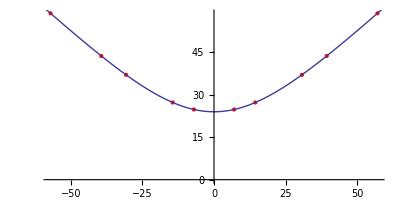

```mathematica
Show[{
	ListPlot[Map[{xOrig[#],yOrig[#]}&,tValues//Flatten],AspectRatio->1/2,AxesOrigin->{0,0},PlotStyle->{PointSize->Large,Red}],
	ParametricPlot[{xOrig[t],yOrig[t]},{t,0,1},AspectRatio->1/2,AxesOrigin->{0,0}]
}]
```

```mathematica
Map[(
	tL=#⟦1⟧;
	tR=#⟦2⟧;
	approximationKnots[pathAdjacent[knotsOrig,lineWidth],tL,tR,1/16,1/16]//MatrixForm
)&,Take[tValues,5]]
```

curvature0Function = 1340.504847246687058975194594354637465651168197 ≈ 1340.5

curvature1Function = 316.352029416664099723360136488854526050914292 ≈ 316.352

curvature0Bezier = -(11337.3595861610895086885790045108499 s1$1031 Abs[s1$1031])/(-0.0452863575055156077606902810937730029+1. s2$1031) ≈ -(11337.4 s1$1031 Abs[s1$1031])/(-0.0452864+1. s2$1031)

curvature1Bezier = -(5981.9175651481637149924554271901378 s2$1031 Abs[s2$1031])/(-0.058122154846031463121571794249756351+1. s1$1031) ≈ -(5981.92 s2$1031 Abs[s2$1031])/(-0.0581222+1. s1$1031)

slv = {s1$1031→0.0352608267860169967,s2$1031→0.0347708917062619174} ≈ {s1$1031→0.0352608,s2$1031→0.0347709}

curvature0Function = 171.520004365502631098072525656512685869535547 ≈ 171.52

curvature1Function = 60.4793258584088535935202983697916728798785867 ≈ 60.4793

curvature0Bezier = -(1496.95717206746284321120745410338128 s1$1359 Abs[s1$1359])/(-0.0592144202832969631305646546990888777+1. s2$1359) ≈ -(1496.96 s1$1359 Abs[s1$1359])/(-0.0592144+1. s2$1359)

curvature1Bezier = -(836.96953945994028719640655051679448 s2$1359 Abs[s2$1359])/(-0.06881458864973925442761656162788124+1. s1$1359) ≈ -(836.97 s2$1359 Abs[s2$1359])/(-0.0688146+1. s1$1359)

slv = {s1$1359→0.0443194431580189191,s2$1359→0.0420715639073118345} ≈ {s1$1359→0.0443194,s2$1359→0.0420716}

curvature0Function = 43.9815335848555746540044030103385524222529565 ≈ 43.9815

curvature1Function = 43.9815335848555746540044030103385524222529565 ≈ 43.9815

curvature0Bezier = -(493.789058763625142897001698908281213 s1$1688 Abs[s1$1688])/(-0.0651922226228522937848468418659008189+1. s2$1688) ≈ -(493.789 s1$1688 Abs[s1$1688])/(-0.0651922+1. s2$1688)

curvature1Bezier = -(493.78905876362514289700169890828121 s2$1688 Abs[s2$1688])/(-0.065192222622852293784846841865900819+1. s1$1688) ≈ -(493.789 s2$1688 Abs[s2$1688])/(-0.0651922+1. s1$1688)

slv = {s1$1688→0.0437261255504949018,s2$1688→0.0437261255504949018} ≈ {s1$1688→0.0437261,s2$1688→0.0437261}

curvature0Function = 60.4793258584088535935202983697916728798785867 ≈ 60.4793

curvature1Function = 171.52000436550263109807252565651268586953555 ≈ 171.52

curvature0Bezier = -(836.969539459940287196406550516794476 s1$2016 Abs[s1$2016])/(-0.0688145886497392544276165616278812403+1. s2$2016) ≈ -(836.97 s1$2016 Abs[s1$2016])/(-0.0688146+1. s2$2016)

curvature1Bezier = -(1496.95717206746284321120745410338128 s2$2016 Abs[s2$2016])/(-0.0592144202832969631305646546990888777+1. s1$2016) ≈ -(1496.96 s2$2016 Abs[s2$2016])/(-0.0592144+1. s1$2016)

slv = {s1$2016→0.0420715639073118345,s2$2016→0.0443194431580189191} ≈ {s1$2016→0.0420716,s2$2016→0.0443194}

curvature0Function = 316.35202941666409972336013648885452605091429 ≈ 316.352

curvature1Function = 1340.5048472466870589751945943546374656511682 ≈ 1340.5

curvature0Bezier = -(5981.9175651481637149924554271901378 s1$2344 Abs[s1$2344])/(-0.0581221548460314631215717942497563512+1. s2$2344) ≈ -(5981.92 s1$2344 Abs[s1$2344])/(-0.0581222+1. s2$2344)

curvature1Bezier = -(11337.3595861610895086885790045108499 s2$2344 Abs[s2$2344])/(-0.0452863575055156077606902810937730029+1. s1$2344) ≈ -(11337.4 s2$2344 Abs[s2$2344])/(-0.0452864+1. s1$2344)

slv = {s1$2344→0.0347708917062619174,s2$2344→0.0352608267860169967} ≈ {s1$2344→0.0347709,s2$2344→0.0352608}

{(-63. | -56.3884000943525182 | -50.4527467803763288 | -45.
52.011389607960151085629572513701170183678292 | 46.209889347766337 | 41.1166949302958521 | 36.712919337619429706712522314009749136179121192),(-36. | -29.5756972912269521 | -23.7017354997779966 | -18.
29.77012457630582549987448713346521030462545282 | 25.0886340477643463 | 21.4919438804816081 | 19.015061681124395820492250581522059217134953899),(-9. | -2.9634650557763704 | 2.9634650557763704 | 9.
16.02273667369403414478339250581732621926599281 | 14.65881340191803651 | 14.65881340191803651 | 16.02273667369403414478339250581732621926599281),(18. | 23.7017354997779966 | 29.5756972912269521 | 36.
19.0150616811243958204922505815220592171349539 | 21.4919438804816081 | 25.0886340477643463 | 29.77012457630582549987448713346521030462545282),(45. | 50.4527467803763288 | 56.3884000943525182 | 63.
36.71291933761942970671252231400974913617912119 | 41.1166949302958521 | 46.209889347766337 | 52.011389607960151085629572513701170183678292)}

^2